# FORMERLY_Math v1.0

## Initializing

### Package

```mathematica
Needs["NDSolve`FEM`"];
```

```mathematica
Needs["Notation`"];
```

### Symbols

```mathematica
Symbolize[𝒮^i_];AddInputAlias["Si"->𝒮^□];
```

```mathematica
Symbolize[Subscript[𝒞, 𝒮^i_]];AddInputAlias["CSi"->𝒞_(𝒮^□)];
```

```mathematica
Symbolize[Subscript[ℛ, 𝒮^i_]];AddInputAlias["RSi"->ℛ_(𝒮^□)];
```

```mathematica
Symbolize[Subscript[ℐ, 𝒮^i_]];AddInputAlias["ISi"->ℐ_(𝒮^□)];
```

```mathematica
Symbolize[Subscript[Ω, 𝒮^i_]];AddInputAlias["WSi"->Ω_(𝒮^□)];
```

```mathematica
Symbolize[Subscript[Γ, 𝒮^i_]];AddInputAlias["GSi"->Γ_(𝒮^□)];
```

```mathematica
Symbolize[Subscript[f, 𝒮^i_]];AddInputAlias["fSi"->f_(𝒮^□)];
```

```mathematica
Symbolize[Subscript[f, 𝒮^i_]];AddInputAlias["$fSi"->f_(𝒮^□)];
```

```mathematica
Symbolize[Subscript[a, i_]];AddInputAlias["lai"->a_■]
```

```mathematica
Symbolize[Subscript[a, i]];AddInputAlias["la"->Subscript[a, i]]
```

```mathematica
Symbolize[a^i_];AddInputAlias["uai"->a^■]
```

```mathematica
Symbolize[a^i];AddInputAlias["ua"->a^i]
```

```mathematica
Symbolize[Subscript[F, 𝒮^i_]];AddInputAlias["FSi"->F_(𝒮^□)];
```

```mathematica
Symbolize[Subscript[F, 𝒮^i_]];AddInputAlias["$FSi"->F_(𝒮^□)];
```

```mathematica
Symbolize[S^{i_,j_}];AddInputAlias["SPu"->S^{■,□}]
```

```mathematica
Symbolize[S̃];AddInputAlias["pS"->S̃]
```

```mathematica
Symbolize[(S̃)^{i_,j_}];AddInputAlias["pSPu"->(S̃)^{■,□}]
```

```mathematica
Symbolize[Subscript[î, a_]];AddInputAlias["lia"->î_■]
Symbolize[î^a_];AddInputAlias["uia"->î^■]
```

```mathematica
Symbolize[x^_];AddInputAlias["x^"->x^□];
Symbolize[Subscript[x, _]];AddInputAlias["x_"->x_□];
OverTilde[x][i_/;i>0&&IntegerQ[i]]:=ToExpression[SuperscriptBox["x",ToString[i]]]
OverTilde[x][i_/;i<0&&IntegerQ[i]]:=ToExpression[SubscriptBox["x",ToString[Abs[i]]]]
```

```mathematica
Symbolize[a_(..)];Symbolize[a^(..)];
```

```mathematica
mod[u_]:=Sqrt[u.u]
```

## Data

#### Planform data [m]

```mathematica
b=4.;
l=6.5;
```

#### Boundary arches height [m]

```mathematica
h=0.8;
```

#### Shell Thickness [m]

```mathematica
t=0.12;
```

#### Shell Material and weight

```mathematica
Subscript[ρ, a]=18.0; (*kN/m^3*)
w=Subscript[ρ, a] t; (*kN/m^2*)
```

#### FEM Mesh Size

```mathematica
size=0.5;
```

## Domine and Airy Stress Function Definition

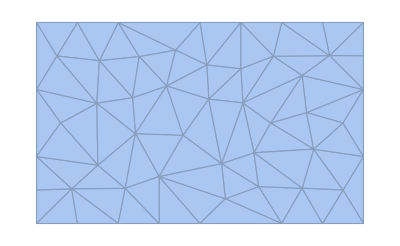

```mathematica
ℛ=ImplicitRegion[-l/2≤ x1≤ l/2&&-b/2≤ x2≤ b/2, {{x1,-l/2,l/2},{x2,-b/2,b/2}}];
Ω=DiscretizeRegion[ℛ,"MeshOrder"->2,MaxCellMeasure->size];
CentroidMeshPoints=AnnotationValue[{Ω,2},MeshCellCentroid];
Show[Ω]
```

### Airy Stress Function

```mathematica
A[σ_,α_]:={{x1,x2,σ(1/8(1(b^2-4x2^2)+α(l^2-4x1^2)))},{x1,x2}∈Ω}
```

## Boundary Conditions Γ_(𝒮^i)

### Arch in x_1 direction (Γ_(𝒮^0))

```mathematica
Subscript[Γ, 𝒮^0]=0;
```

### Arch in x_1 direction (Γ_(𝒮^1))

```mathematica
EqCircle[x1_,x3_]=(x1-x10)^2+(x3-x30)^2==r^2;
```

```mathematica
MyCircle[pt1_,pt2_,pt3_]:=EqCircle[x1,x3]/.First[Solve[{EqCircle@@pt1,EqCircle@@pt2,EqCircle@@pt3,r>0},{x10,x30,r}]//Quiet]
```

```mathematica
Intradox=MyCircle[{-l/2,0},{0,h},{l/2,0}];
```

```mathematica
solI=Solve[Intradox,x3]//Quiet;
```

```mathematica
Subscript[Γ, 𝒮^1]=x3/.solI[[2]];
```

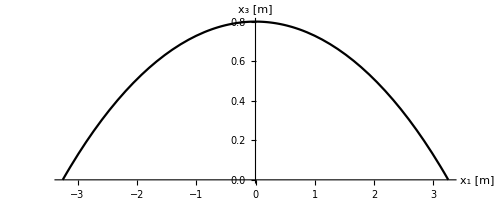

```mathematica
bsc1Plot=Plot[Subscript[Γ, 𝒮^1],{x1,-l/2,l/2}, AxesStyle->Directive[Black, 16],LabelStyle->Directive[FontFamily->"Times"],PlotStyle->Black,AxesLabel->{"x_1 [m]","x_3 [m]"},AspectRatio->Automatic]
```

### Arches in x_1 and x_2 direction (Γ_(𝒮^2))

```mathematica
Subscript[Γ, 𝒮^2]=h+(-(2h/b^2)(x1^2+x2^2));
```

```mathematica
Plot3D[(*{x1,x2,Subscript[Γ, 𝒮^2]}*)Subscript[Γ, 𝒮^2],{x1,x2}∈Ω,LabelStyle->Directive[FontFamily->"Times"],PlotPoints->100,PlotStyle->Directive[Gray,Opacity[0.0]],Mesh->None,BoundaryStyle->Thickness[0.005],AxesLabel->{"x_1[m]","x_2[m]","x_3[m]"},BoxRatios->Automatic,Boxed->False, AxesStyle->Directive[Black, 16],AxesOrigin->{-l/2,b/2,0},Boxed->False,ViewPoint->{2,-2,2},ViewCenter->Automatic]
```

-Graphics3D-

## Transversal Equilibrium Equation Solution

#### Second derivate of F

```mathematica
Subscript[F, 𝒮22]=D[A[σ,α][[1,3]], {x2,2}];
Subscript[F, 𝒮11]=D[A[σ,α][[1,3]], {x1,2}];
Subscript[F, 𝒮12]=D[A[σ,α][[1,3]], x1,x2];
```

#### Differential equation (𝒻 unknown)

```mathematica
EqDiff[σ_,α_]=((D[Subscript[f, 𝒮^1][x1,x2],{x2,2}] Subscript[F, 𝒮11]+
D[Subscript[f, 𝒮^1][x1,x2],{x1,2}] Subscript[F, 𝒮22]-
2 D[Subscript[f, 𝒮^1][x1,x2],x1,x2] Subscript[F, 𝒮12])-w);
```

#### Boundary conditions

```mathematica
bcs[0]=DirichletCondition[Subscript[f, 𝒮^1][x1,x2]==Subscript[Γ, 𝒮^0],True];
bcs[1]=DirichletCondition[Subscript[f, 𝒮^1][x1,x2]==Subscript[Γ, 𝒮^1],True];
bcs[2]=DirichletCondition[Subscript[f, 𝒮^1][x1,x2]==Subscript[Γ, 𝒮^2],True];
```

#### Equilibrium solution

```mathematica
Subscript[h, 𝒮^1]=Subscript[f, 𝒮^1]/.ParametricNDSolve[
{EqDiff[σ,α]==0,bcs[1]},Subscript[f, 𝒮^1],{x1,x2}∈Ω,{σ,α},
Method->{"FiniteElement",
"MeshOptions"->{"MeshOrder"->2,MaxCellMeasure->size},
"IntegrationOrder"->4,
"InterpolationOrder"->{Subscript[f, 𝒮^1]->2}}];
```

```mathematica
𝒻[σ_,α_]=(Subscript[h, 𝒮^1][σ,α])[x1,x2];
```

## Reference surface selection

```mathematica
Manipulate[Plot3D[{Evaluate[𝒻[σ,α]]},{x1,x2}∈Ω, LabelStyle->Directive[FontFamily->"Times"],AxesStyle->Directive[Black, 16],PlotPoints->Automatic,PlotStyle->Directive[Gray,Opacity[0.5]],Mesh->True,BoundaryStyle->Thickness[0.003],AxesLabel->{"x_1 [m]","x_2 [m]","x_3 [m]"},BoxRatios->Automatic,AxesOrigin->{-l/2,b/2,0},Boxed->False,ViewPoint->{2,-2,2},ViewCenter->Automatic],{{σ,3.9},.01,20.},
{{α,0.8},0.1,3.0}]
```

```mathematica
RuleSol = {σ→3.9,α→0.8};
```

```mathematica
𝒻𝓇=𝒻[σ,α]/.RuleSol;
RefShell=Plot3D[𝒻𝓇,{x1,x2}∈Ω,LabelStyle->Directive[FontFamily->"Times"],PlotPoints->100,PlotStyle->Directive[Gray,Opacity[0.5]],Mesh->True,BoundaryStyle->Thickness[0.003],AxesLabel->{"x_1[m]","x_2[m]","x_3[m]"},BoxRatios->Automatic,Boxed->False, AxesStyle->Directive[Black, 16],AxesOrigin->{-l/2,b/2,0},Boxed->False,ViewPoint->{2,-2,2},ViewCenter->Automatic]
```

-Graphics3D-

## 2^nd Solution (load assigned on the membrane shape)

## Constrained Form Finding

### Real Load Evaluation

#### Shell and its derivative

```mathematica
𝒻1=D[𝒻𝓇, x1];
𝒻2=D[𝒻𝓇, x2];
```

#### Cartesian unit base vectors

```mathematica
Subscript[e, 1]={1,0,0};
Subscript[e, 2]={0,1,0};
Subscript[e, 3]={0,0,1};
```

#### Shell Basis and Jacobian

```mathematica
Subscript[a, 1]=Subscript[e, 1]+𝒻1 Subscript[e, 3];
Subscript[a, 2]=Subscript[e, 2]+𝒻2 Subscript[e, 3];
J=mod[Subscript[a, 1]×Subscript[a, 2]]//Simplify;
Subscript[a, 3]=(Subscript[a, 1]×Subscript[a, 2])/J//Simplify;
```

#### Exact Shell Load

```mathematica
p=w J;
```

```mathematica
LoadProfile1=Plot3D[p,{x1,x2}∈Ω,LabelStyle->Directive[16,Black,FontFamily->"Times"],PlotRange->All,BoundaryStyle->Directive[Darker[Green],Thickness[0.003]],PlotStyle->Directive[Lighter[Green],Opacity[0.8]],AxesLabel->{"x_1 [m]","x_2 [m]","p [kN/m]"},LabelStyle->Directive[Black, 16],PlotPoints->100,AxesOrigin->{-l/2,b/2,0},Boxed->False,ViewPoint->{2,-2,2},ViewCenter->Automatic]//Quiet
```

-Graphics3D-

### Solution

#### Differential equation (𝒻 unknown)

```mathematica
EqDiff2[σ_,α_]=((D[Subscript[f, 𝒮^2][x1,x2],{x2,2}] Subscript[F, 𝒮11]+
D[Subscript[f, 𝒮^2][x1,x2],{x1,2}] Subscript[F, 𝒮22]-
2 D[Subscript[f, 𝒮^2][x1,x2],x1,x2] Subscript[F, 𝒮12])-p)//Simplify//Chop//N;
```

#### Boundary conditions

```mathematica
bcs2[0]=DirichletCondition[Subscript[f, 𝒮^2][x1,x2]==Subscript[Γ, 𝒮^0],True];
bcs2[1]=DirichletCondition[Subscript[f, 𝒮^2][x1,x2]==Subscript[Γ, 𝒮^1],True];
bcs2[2]=DirichletCondition[Subscript[f, 𝒮^2][x1,x2]==Subscript[Γ, 𝒮^2],True];
```

#### Equilibrium solution

```mathematica
Subscript[h, 𝒮^2]=Subscript[f, 𝒮^2]/.ParametricNDSolve[
{EqDiff2[σ,α]==0,bcs2[1]},Subscript[f, 𝒮^2],{x1,x2}∈Ω,{σ,α},
Method->{"FiniteElement",
"MeshOptions"->{"MeshOrder"->2,MaxCellMeasure->size},
"IntegrationOrder"->4,
"InterpolationOrder"->{Subscript[f, 𝒮^2]->2}}];
```

### Minimization of σ and α

```mathematica
pippo[σ_?NumericQ,α_?NumericQ]:=Module[{h,ω},
h=Subscript[h, 𝒮^2][σ,α][x1,x2];
ω=Ω;
NIntegrate[((h/𝒻𝓇)-1)^2,{x1,x2}∈ω]
]//Simplify//Chop//N
```

```mathematica
sol=Assuming[α>0,NMinimize[
pippo[σ,α],
{{σ,5.2,5.3},{α,0.5,0.6}},WorkingPrecision->2]]//Quiet
```

{0.0017,{σ→5.26581,α→0.515855}}

```mathematica
DistPerc=sol[[1]] 100 "%"
```

0.17 %

#### THRUST SURFACE 𝒻𝓉

```mathematica
𝒻𝓉[σ_,α_]=(Subscript[h, 𝒮^2][σ,α])[x1,x2];
𝒻𝓉=𝒻𝓉[σ,α]/.sol[[2]];
```

```mathematica
FinalShell=Plot3D[𝒻𝓉,{x1,x2}∈Ω,LabelStyle->Directive[FontFamily->"Times"],PlotPoints->100,PlotStyle->Directive[Red,Opacity[0.3]],Mesh->True,BoundaryStyle->Thickness[0.003],AxesLabel->{"x_1 [m]","x_2 [m]","x_3 [m]"},BoxRatios->Automatic,Boxed->False, AxesStyle->Directive[Black, 16],AxesOrigin->{-l/2,b/2,0},Boxed->False,ViewPoint->{2,-2,2},ViewCenter->Automatic]
```

-Graphics3D-

```mathematica
Show[FinalShell,RefShell]
```

-Graphics3D-

## Membrane Stresses

#### 𝒻 and its derivative

```mathematica
𝒻𝓉1=D[𝒻𝓉, x1];
𝒻𝓉2=D[𝒻𝓉, x2];
```

#### Shell Basis and Jacobian

```mathematica
Subscript[a, 1]=Subscript[e, 1]+𝒻𝓉1 Subscript[e, 3];
Subscript[a, 2]=Subscript[e, 2]+𝒻𝓉2 Subscript[e, 3];
J=mod[Subscript[a, 1]×Subscript[a, 2]]//Simplify;
Subscript[a, 3]=(Subscript[a, 1]×Subscript[a, 2])/J//Simplify;
```

#### Second derivative of F

```mathematica
Subscript[F, 𝒮11]=D[(A[σ,α][[1,3]]/.sol[[2]]),{x1,2}];
Subscript[F, 𝒮22]=D[(A[σ,α][[1,3]]/.sol[[2]]),{x2,2}];
Subscript[F, 𝒮12]=D[(A[σ,α][[1,3]]/.sol[[2]]),x1,x2];
```

#### Stress tensor

```mathematica
S=({{Subscript[F, 𝒮22],-Subscript[F, 𝒮12]},{-Subscript[F, 𝒮12],Subscript[F, 𝒮11]}});MatrixForm[S];
T=(S/J);
TT=(T[[1,1]] TensorProduct[Subscript[a, 1],Subscript[a, 1]]+T[[2,2]] TensorProduct[Subscript[a, 2],Subscript[a, 2]]+T[[1,2]] TensorProduct[Subscript[a, 1],Subscript[a, 2]]+T[[2,1]] TensorProduct[Subscript[a, 2],Subscript[a, 1]])//N;
```

```mathematica
EigSyst=Eigensystem[TT];
tmpVal=EigSyst[[1]];
tmpVect=EigSyst[[2]];
```

```mathematica
valMax=tmpVal[[3]];
valMin=tmpVal[[2]];
```

```mathematica
vecMax=tmpVect[[1,{1,2}]];
vecMin=tmpVect[[2,{1,2}]];
```

#### Stresses plot (membrane)

```mathematica
EigenValMax=DensityPlot[-(0.001 valMax/t),{x1,x2}∈Ω,
PlotPoints->150,
FrameLabel->{"x_1 [m]","x_2 [m]"},
LabelStyle->Directive[Black,16,FontFamily->"Times"],
Mesh->None,
ColorFunction-> "TemperatureMap",
AspectRatio->Automatic,
PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"σ_max [MPa]"],BoundaryStyle->Black
]//Quiet
```

-Graphics-

```mathematica
EigenValMin=DensityPlot[-(0.001 valMin/t),{x1,x2}∈Ω,
PlotPoints->150,
FrameLabel->{"x_1 [m]","x_2 [m]"},
LabelStyle->Directive[Black,16,FontFamily->"Times"],
Mesh->None,
ColorFunction-> "TemperatureMap",
AspectRatio->Automatic,
PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"σ_min [MPa]"],BoundaryStyle->Black
]//Quiet
```

-Graphics-

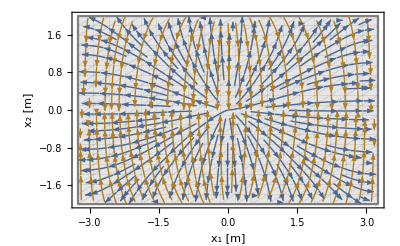

```mathematica
EigenVec=StreamPlot[{vecMax,vecMin},{x1,x2}∈Ω,RegionBoundaryStyle->{Gray},RegionFillingStyle->{Lighter[Gray]},AspectRatio->Automatic,FrameLabel->{"x_1 [m]","x_2 [m]"},FrameStyle->Directive[Black, 16,FontFamily->"Times"],RegionBoundaryStyle->True,PerformanceGoal->"Quality",RegionFillingStyle->True]//Quiet
```